# EEMB 595TE Fall 2021

## Task 1: population with random migration and immigration

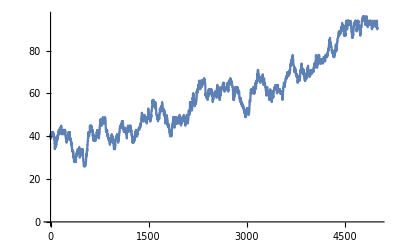

```mathematica
(*clear previous simulations*)
Clear[n];
(*initial population*)
n[0]=40;
(*probability of 1 individual leaving*)
α=.2;
(*probability of 1 individual arriving*)
β=.2;
(*time steps*)
tmax=5000;
(*migration and immigration*)
migration:=RandomVariate[BernoulliDistribution[β]];
immigration:=RandomVariate[BernoulliDistribution[α]];
(*update step*)
n[t_]:=n[t]=Max[0,n[t-1]-immigration+migration];
(*simulate*)
data=Table[n[t],{t,0,tmax}];
(*simulate and plot*)
ListPlot[data,Joined->True,PlotRange->Full]
```